# Моделирование движения спускаемого аппарата в атмосфере

## Интегрированные математические пакеты

Самарский университет. Кафедра теоретической механики

Юдинцев В. В.

## Модель

Рассматривается движение спускаемого аппарата в атмосфере Земли.

-Graphics-

## Условия

Вращение Земли не учитывается

Спускаемый аппарат рассматривается как материальная точка постоянной массы

Рассматривается движение спускаемого в одной плоскости

Движение спускаемого аппарата происходит под действием силы тяжести и сил аэродинамического сопротивления

## Аэродинамические силы

На спускаемый аппарат при движении в атмосфере действуют аэродинамические силы и моменты. 

Аэродинамические силы и моменты зависят от следующих параметров:
- угла атаки спускаемого аппарата;
- плотности воздуха на высоте полета;
- размеров спускаемого аппарата;
- формы спускаемого аппарата.

## Аэродинамические силы

### Представление аэродинамических сил

F_D=C_D(M,α)×S×(ρ V^2)/2
F_L=C_L(M,α)×S×(ρ V^2)/2

S 	- площадь Миделя (характерная площадь) спускаемого аппарата
V 	- скорость набегающего потока воздуха
ρ 	- плотность воздуха (зависит от высоты полёта)
M 	- число Маха: отношение скорости набегающего потока воздуха к местной скорости  звука
C_D 	-  коэффициент лобового сопротивления, зависящий от M, α, условий обтекания 
C_L 	-  коэффициент подъемной силы сопротивления, зависящий от M, α, условий обтекания

Скоростной напор (имеет размерность давления)

q = (ρ V^2)/2 [Па]

## Аэродинамические характеристики

### Спускаемый аппарат космического корабля “Союз”

Масса: 3000 кг

-Graphics-

Claus Weiland 
Aerodynamic Data of Space Vehicles
Springer Heidelberg New York Dordrecht London, 2014.

## Аэродинамические характеристики

-Graphics-

-Graphics-

## Плотность воздуха

Зависимость плотности воздуха от высоты может быть определена при помощи термодинамической модели атмосферы, экспериментальных данных.

```mathematica
StandardAtmosphereData[Quantity[10000,"Feet"],"Density",Method->"USStandardAtmosphere"]
%//QuantityMagnitude
```

0.904848 kg/m^3

0.904848

```mathematica
ρ=.;
ρ[h_]:=QuantityMagnitude[StandardAtmosphereData[Quantity[h,"Meters"],"Density",Method->"USStandardAtmosphere"]];
```

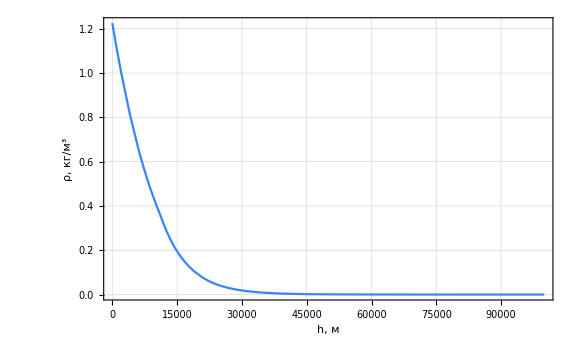

```mathematica
Plot[ρ[h],{h,0,100000},PlotRange->All,PlotTheme->{"Presentation","FrameGrid"},FrameLabel->{ "h, м","ρ, кг/(:043c)^3"} ,ImageSize->Large]
```

```mathematica
Quantity[a, "Meters"]*Quantity[b, "Newtons"]
```

a b m N

## Загрузка таблицы из файла

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["atm.txt"];
```

```mathematica
data=Import["atm.txt","table"];
```

```mathematica
(data[[3;;,{1,7}]])
```

{{-2,1.478},{0,1.225},{2,1.007},{4,0.8193},{6,0.6601},{8,0.5258},{10,0.4135},{12,0.3119},{14,0.2279},{16,0.1665},{18,0.1216},{20,0.08891},{22,0.06451},{24,0.04694},{26,0.03426},{28,0.02508},{30,0.01841},{32,0.01355},{34,0.009887},{36,0.007257},{38,0.005366},{40,0.003995},{42,0.002995},{44,0.002259},{46,0.001714},{48,0.001317},{50,0.001027},{52,0.0008055},{54,0.0006389},{56,0.0005044},{58,0.0003962},{60,0.0003096},{62,0.0002407},{64,0.000186},{66,0.0001429},{68,0.0001091},{70,0.00008281},{72,0.00006236},{74,0.00004637},{76,0.0000343},{78,0.00002523},{80,0.00001845},{82,0.00001341},{84,9.69×10^-6},{86,6.955×10^-6}}

```mathematica
ρ=Interpolation[%]
```

InterpolatingFunction[…]

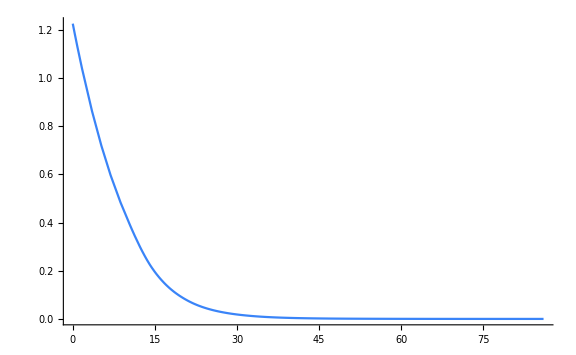

```mathematica
Plot[ρ[h],{h,0,86},PlotRange->All]
```

Исправить (самостоятельно)
- Таблица слишком “короткая” (до 86 км)
- Высота в километрах. В уравнениях  движения высота в метрах.

```mathematica
SetOptions[Plot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
SetOptions[ParametricPlot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
SetOptions[ListPlot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
```

## Уравнения движения

Уравнения движения

```mathematica
q={V[t],r[t],θ[t],s[t]};
```

```mathematica
eq={
V'[t]==-g Sin[θ[t]]-Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
V[t] θ'[t]==g(V[t]^2/(r[t] g)-1)Cos[θ[t]]+Subscript[c, L] S(ρ[r[t]-Rz] V[t]^2)/(2 m),
s'[t]==V[t]/r[t] Cos[θ[t]] Rz, 
r'[t]==V[t] Sin[θ[t]]
};
```

Вывод уравнений приведен в книге:
В. А. Ярошевский Вход в атмосферу космических летательных аппаратов
М.: Наука, 1988, стр. 24.

## Параметры системы

```mathematica
params={Subscript[c, d]->1.5,Subscript[c, L]->0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0}
```

{c_d→1.5,c_L→0,S→3.80133,m→3000.,g→9.807,Rz→6.371×10^6,h0→100000.}

```mathematica
nu={V[0]==7000,θ[0]==0,r[0]==Rz+h0,s[0]==0};
```

Круговая скорость на высоте h0

```mathematica
√(μ/(Rz+h0))/.μ->398600.4415 10^9//.params
```

7848.44

```mathematica
params={Subscript[c, d]->1.3,Subscript[c, L]->0.3,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9}
nu={V[0]==√(μ/(Rz+h0)),θ[0]==0,r[0]==Rz+h0,s[0]==0};
```

{c_d→1.3,c_L→0.3,S→3.80133,m→3000.,g→9.807,Rz→6.371×10^6,h0→100000.,μ→3.986×10^14}

Ускорение свободного падения зависит от высоты полета. 
Например, на высоте h0:

```mathematica
μ/(Rz+h0)^2//.params
```

9.51908

```mathematica
ρ[100000]
```

5.604×10^-7

## Результаты интегрирования

Проинтегрируем уравнения движения до 450 секунды полета

```mathematica
tk=1040;
sol=NDSolve[{eq,nu}//.params,q,{t,0,tk}]
```

{{V[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],s[t]→InterpolatingFunction[…][t]}}

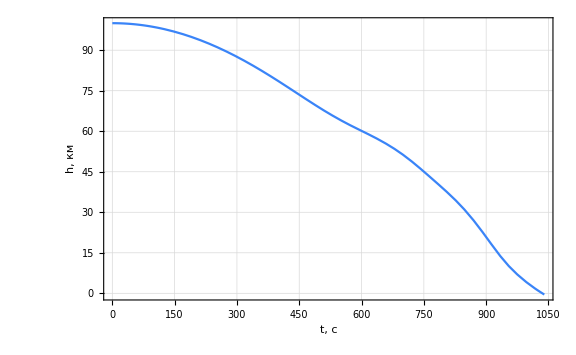

```mathematica
Plot[(r[t]-Rz)*0.001/.params/.sol,{t,0,tk},FrameLabel->{"t, c","h, км"}]
```

Конечная высота

```mathematica
(r[t]-Rz)*0.001/.params/.sol/.t->tk
```

{-0.457104}

## Результаты интегрирования

Траектория от дистанции полета (по поверхности Земли)

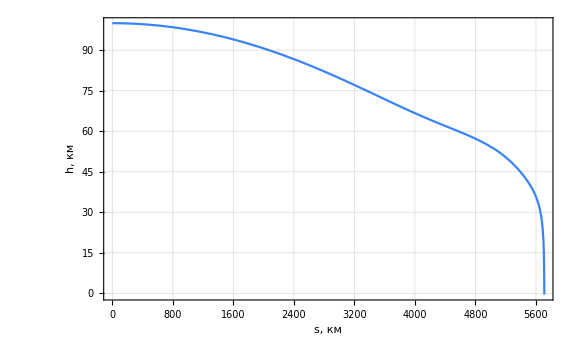

```mathematica
ParametricPlot[{s[t],(r[t]-Rz)}*0.001/.params/.sol,{t,0,tk},FrameLabel->{"s, км","h, км"},AspectRatio->1/GoldenRatio,PlotRange->All]
```

## Результаты интегрирования

Траектория от дистанции полета (по поверхности Земли)

```mathematica
Animate[ParametricPlot[{s[t],(r[t]-Rz)}*0.001/.params/.sol,{t,0,tk},FrameLabel->{"s, км","h, км"},AspectRatio->1/GoldenRatio,Epilog->{Red,PointSize[0.02],Point[{s[t],(r[t]-Rz)}*0.001/.params/.sol/.t->tt]}],{tt,0,tk}]
```

## Результаты интегрирования

Скорость от высоты

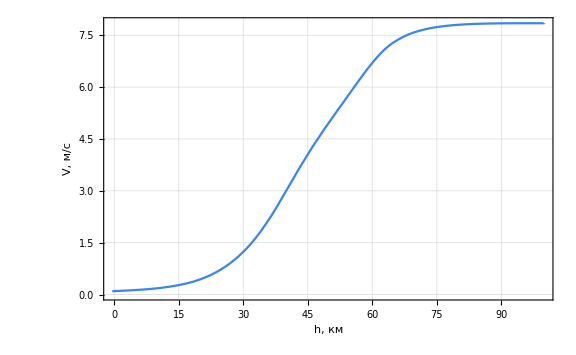

```mathematica
ParametricPlot[{(r[t]-Rz), V[t]}*0.001/.params/.sol,{t,0,tk},FrameLabel->{"h, км","V, м/c"},AspectRatio->1/GoldenRatio]
```

## Управление процессом интегрирования

Остановка процесса численного интегрирования при достижении нулевой высоты.
Функция WhenEvent

```mathematica
tk=1100;
sol=NDSolve[
{
eq,nu,WhenEvent[r[t]<Rz//.params,"StopIntegration"]
}//.params,q,{t,0,tk}
]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1035.2 and t = 1035.25.

{{V[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],s[t]→InterpolatingFunction[…][t]}}

```mathematica
tk=sol[[1,1,2,0,1,1,2]]
```

1035.22

Конечная высота

```mathematica
r[t]-Rz/.sol/.params/.t->tk
```

{-9.12696×10^-8}

## Управление процессом интегрирования

Остановка процесса численного интегрирования при достижении нулевой высоты.
Функция WhenEvent

```mathematica
conditions=r[t]<Rz+#&/@Range[0, 50000, 10000]
```

{r[t]<Rz,r[t]<10000+Rz,r[t]<20000+Rz,r[t]<30000+Rz,r[t]<40000+Rz,r[t]<50000+Rz}

```mathematica
tk=1100;
{sol,velocities}=Reap[NDSolve[
{
eq,nu,WhenEvent[Evaluate[conditions//.params],{Sow[V[t]],If[Abs[r[t]-Rz]<10//.params,"StopIntegration","CrossDiscontinuity"]}]
}//.params,q,{t,0,tk}
]
]
```

{{{V[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],s[t]→InterpolatingFunction[…][t]}},{{4990.16,3004.33,1235.3,440.515,180.777,99.6276}}}

```mathematica
velocities
```

{{4990.16,3004.33,1235.3,440.515,180.777,99.6276}}

```mathematica
tk=sol[[1,1,2,0,1,1,2]]
```

1035.22

```mathematica
Reap[Sum[Sow[i^2]+1,{i,10}]]
```

{395,{{1,4,9,16,25,36,49,64,81,100}}}

## Траектория спуска

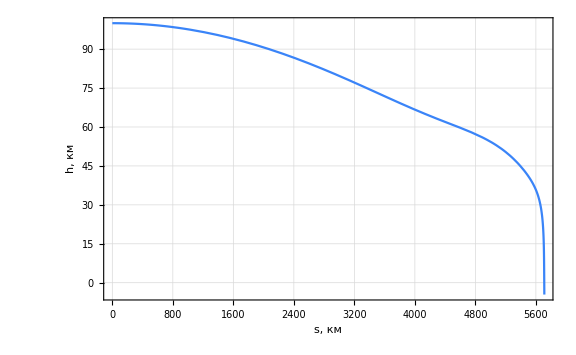

```mathematica
ParametricPlot[{s[t],(r[t]-Rz)}*0.001/.params/.sol,{t,0,tk},FrameLabel->{"s, км","h, км"},AspectRatio->1/GoldenRatio]
```

## Аэродинамическая сила

Аэродинамическая сила лобового сопротивления

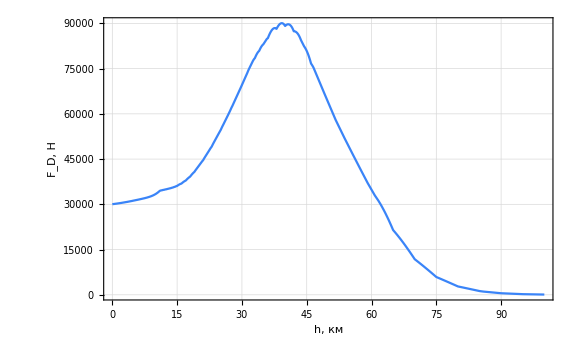

```mathematica
ParametricPlot[{(r[t]-Rz)*0.001,Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/2}//.params/.sol,{t,0,tk},AspectRatio->1/GoldenRatio,FrameLabel->{"h, км","F_D, Н"},PlotRange->All]
```

## Аэродинамическая сила

Максимум аэродинамической силы на траектории спускаемого аппарата

```mathematica
FindMaximum[Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/2/.params/.sol/.t->tt,{tt,100.0}]
Famax=%[[1]];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{90064.1,{tt→793.1}}

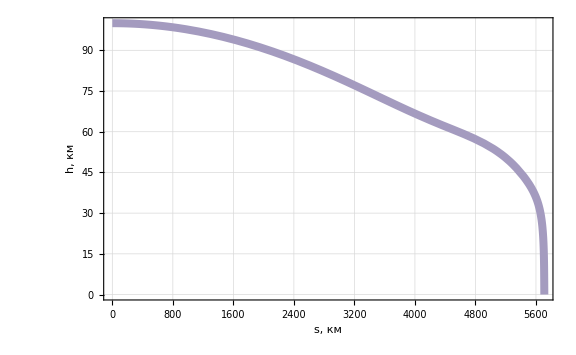

```mathematica
ParametricPlot[Flatten[{s[t],(r[t]-Rz)}]*0.001/.params/.sol,{t,0,tk},FrameLabel->{"s, км","h, км"},AspectRatio->1/GoldenRatio,ColorFunction->(ColorData["TemperatureMap"][Subscript[c, d] S(ρ[r[t]-Rz] V[t]^2)/(2 Famax)//.params/.sol[[1]]/.t->#3]&),ColorFunctionScaling->False,PlotStyle->Thickness[0.01]]
```

```mathematica
ColorData["AvocadoColors"][0.5]
```

RGBColor[0.289326, 0.685107, 0.108759]

```mathematica
ColorData["TemperatureMap"][1]
```

RGBColor[0.817319, 0.134127, 0.164218]

## Перегрузка

Перегрузка 
отношение абсолютной величины линейного ускорения, вызванного негравитационными силами, к ускорению свободного падения на поверхности Земли.

В рассматриваемой задаче негравитационные сила только одна -- это аэродинамическая сила

n=(√(F_D^2+F_L^2))/(m g)

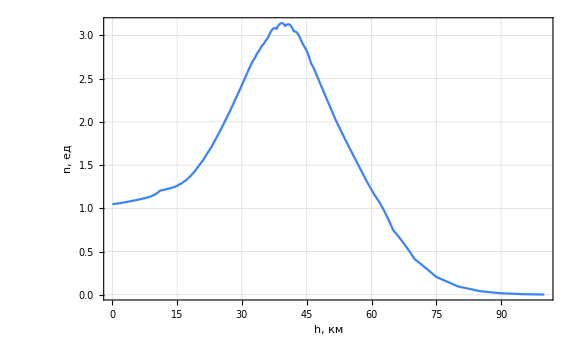

```mathematica
Norm[{Subscript[c, d],Subscript[c, L]}S(ρ[r[t]-Rz] V[t]^2)/2]/(g m);
ParametricPlot[{(r[t]-Rz)*0.001,%}//.params/.sol,{t,0,tk},AspectRatio->1/GoldenRatio,FrameLabel->{"h, км","n, ед"},PlotRange->All]
```

## Задание

1. Модифицируйте программу интегрирования уравнений движения спускаемого аппарата в атмосфере, добавив зависимость плотности воздуха от высоты, загружаемой из файла.

2. Модифицируйте программу интегрирования уравнений движения спускаемого аппарата в атмосфере, добавив зависимость ускорения свободного падения g от высоты. На сколько отличается дальность полета спускаемого аппарата при учете и без учета изменения ускорения свободного падения от высоты полета? 

3. Постройте зависимость максимальной перегрузки, которую испытывает экипаж спускаемого аппарата в зависимости от начального угла входа в атмосферу (θ_0) в диапазоне от минус 15 до 0 градусов.

4. Постройте зависимость дальности точки приземления от начального угла входа в атмосферу (θ_0) в диапазоне от минус 15 до 0 градусов. Нарисуйте на одном графике траектории движения спускаемого аппарата при θ_0=-15^o и при θ_0=-2^o.

## Пример

Функция расстояния до точки приземления в зависимости от начального угла наклона траектории.

```mathematica
dist[θ0_?NumberQ]:=Module[{params,nu,neq,tk,sol},
params={Subscript[c, d]->1.3,Subscript[c, L]->0.0,S->(π 2.2^2)/4,m->3000.0,g->9.807,Rz->6371000.0,h0->100000.0,μ->398600.4415 10^9};
nu={V[0]==√(μ/(Rz+h0)),θ[0]==θ0,r[0]==Rz+h0,s[0]==0};
neq=eq/.params;
sol=NDSolve[{eq,nu,
WhenEvent[r[t]<=Rz//.params,"StopIntegration",DetectionMethod->"Sign"]}//.params,
q,{t,0,5000}];
tk=sol[[1,1,2,0,1,1,2]];
s[t]/.sol/.t->tk
];
```

```mathematica
dist[0.0°]*0.001
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 770.386 and t = 770.455.

{4543.23}

## Пример

```mathematica
Plot[dist[θθ °]*0.001,{θθ,-15,0},PlotRange->All,PlotPoints->2]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 169.047 and t = 169.095.

$Aborted

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 168.962 and t = 169.009.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 174.009 and t = 174.026.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 179.33 and t = 179.567.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

{{-15.,310.788},{-14.,331.567},{-13.,355.192},{-12.,382.32},{-11.,413.825},{-10.,450.9},{-9.,495.215},{-8.,549.187},{-7.,616.44},{-6.,702.676},{-5.,817.404},{-4.,977.74},{-3.,1217.91},{-2.,1617.77},{-1.,2415.02},{0.,4543.23}}

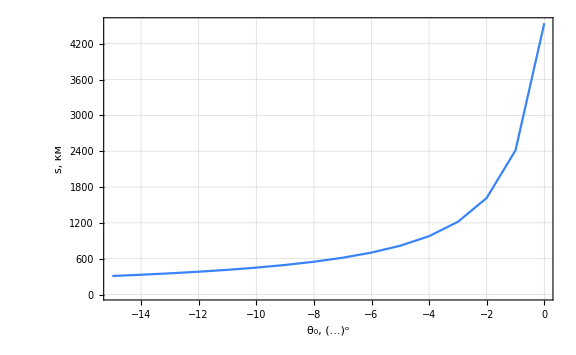

```mathematica
Flatten[{#*180/π,dist[# ]*0.001}]&/@Range[-15.0°,0,1°]
ListPlot[%,FrameLabel->{"θ_0, (...)^o","s, км"},Joined->True]
```